```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
HarmonicTrap1D[];
sizes={4096};
timeStep=0.0001;
k=-0.5;
contactInteractionFactor=4 Pi k;
max=50ho;
min=-50ho;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{4096} | 1 | 4096 | {50} | {-50} | {20/819} | {(819 π)/40960} | {(819 π)/20}

```mathematica
calcAllTable
p1=plotProjections;
```

time | energies | moments | misc
(0) | (total | -0.753314
kinetic | 0.25
potential | 0.25
contact | -1.25331
virial | -1.25331) | (meanX | 0
sigmaX | 0.707107
norm | 1.) | (steps | 0
A0 | 0.751126)

```mathematica
AbsoluteTiming[evolve["ite",10,10]]
```

{74.7602,Null}

time | energies | moments | misc
(10.) | (total | -1.60446
kinetic | 1.72039
potential | 0.0394235
contact | -3.36427
virial | -0.00234572) | (meanX | 0
sigmaX | 0.280797
norm | 1.) | (steps | 100000
A0 | 1.26586)

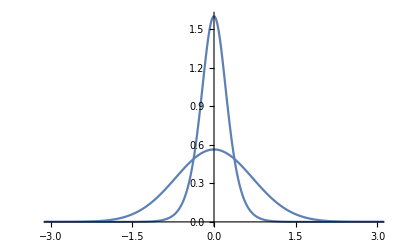

```mathematica
calcAllTable
p2=plotProjections;
Show[p1,p2,PlotRange->{{-3,3},All}]
```

Turn off harmonic potential

```mathematica
plot:=AppendTo[lplots,{time,plotProjections,interp[wf]}];
newPotential[(0&)];
reset;
AbsoluteTiming[evolve["ite",10,10,10]]
```

{70.1773,Null}

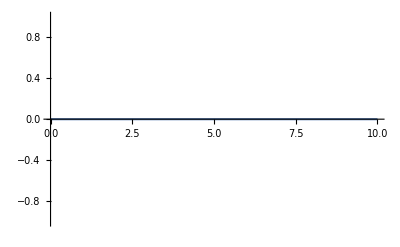
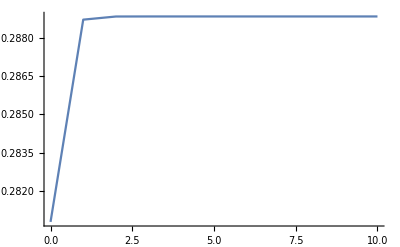

```mathematica
{ListPlot[lmoments[[All,{1,2}]],Joined->True,PlotRange->All],
ListPlot[lmoments[[All,{1,3}]],Joined->True,PlotRange->All]}
```

```mathematica
wfsoliton=wf;
psi=interp[wfsoliton]
wfsoliton2=Map[psi[First[#]]&,mesh[],{dim}];
Chop@Norm[wfsoliton-wfsoliton2]
```

InterpolatingFunction[…]

0

```mathematica
x0=-10;
wfshifted=Map[Piecewise[{{psi[First[#]-x0],Abs[First[#]-x0]<10}},0]&,mesh[],{dim}];
```

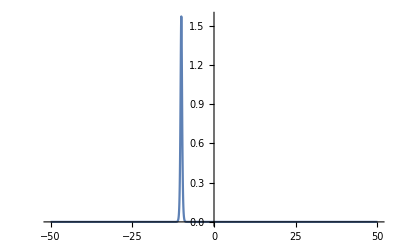

```mathematica
p=3; (* momentum *)
wf=wfshifted*Exp[I p meshX];
ListPlot[projectionX,PlotRange->All,Joined->True]
```

```mathematica
reset;
AbsoluteTiming[evolve["rte",15,50,10]]
```

{136.609,Null}

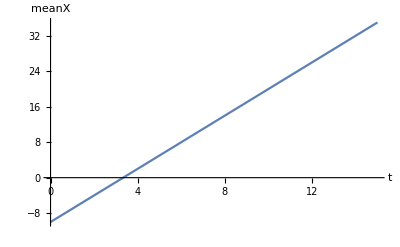

```mathematica
plotM["meanX"]
```

```mathematica
lmstart=listM["meanX"][[1]]
lmend=listM["meanX"][[-1]]
Δt=lmend[[1]]-lmstart[[1]]
Δx=lmend[[2]]-lmstart[[2]]
v=Δx/Δt
```

{0,-9.99999}

{15.,35.}

15.

45.

3.

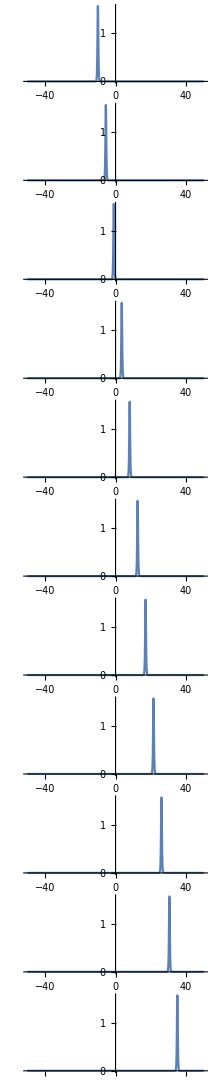

```mathematica
GraphicsGrid[Table[{lplots[[i,2]]},{i,Length[lplots]}],ImageSize->3 72]
```

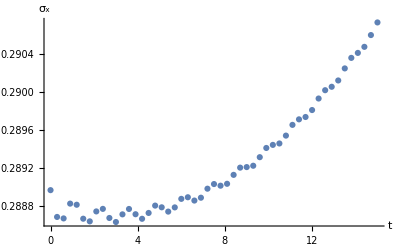

```mathematica
(* The slight broadening of the soliton is a numerical artifact due to a finite step size. *)
l=listM["sigmaX"]^2-listM["meanX"]^2;
l[[All,1]]=listM["sigmaX"][[All,1]];
l[[All,2]]=Sqrt[l[[All,2]]];
ListPlot[l,AxesLabel->{"t","σ_x"}]
```